```mathematica
ClearAll[rho,x,theta,k, prob]
psi[m_,x_]=HermiteH[m,x]/(√(2^m*m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
```

```mathematica
n=10;
```

```mathematica
Tpsi=Table[psi[m,x],{m,0,n+1}];
```

```mathematica
rho=Table[ KroneckerDelta[a,b]/(n+1),{a,0,n},{b,0,n}] ;
(* starting density matrix in the Fock basis *)
```

```mathematica
Proj=Table[(Tpsi[[a+1]]Tpsi[[b+1]])ⅇ^(ⅈ(b-a)theta),{a,0,n},{b,0,n}];
```

```mathematica
prob=∑_(b=0)^n ∑_(a=0)^n rho[[b+1,a+1]]Proj[[a+1,b+1]];
```

```mathematica
Data=Extract[Import["C:/sqzfinal10000.txt","Table"],1];
dataSh=Extract[Import["C:/shotfinal10000.txt","Table"],1];
```

```mathematica
Media=Mean[dataSh]
SQL=StandardDeviation[dataSh]
```

-0.0000434907

0.00322232

```mathematica
(*NB:data must be normalized in order to have the shot noise(=variance of the vacuum) equal to 1/2*)
```

```mathematica
(*check the shot noise variance*)
Variance[(dataSh-Media)/SQL*1/(√2)]
```

0.5

```mathematica
data=(Data-Media)/SQL*1/(√2);
```

```mathematica
ldata=Length[data];
```

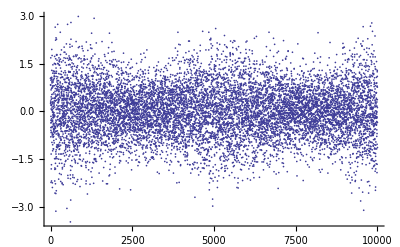

```mathematica
ListPlot[data,PlotStyle->{PointSize[0.003]}]
```

```mathematica
(*create the marginal distributions*)
```

```mathematica
Nbin=100;
```

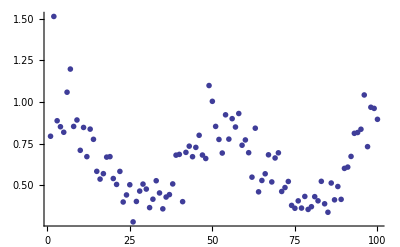

```mathematica
Do[Marginal[j]=Partition[data,10000/Nbin][[j]],{j,1,Nbin}];
Rumore=Table[Variance[Marginal[j]],{j,1,Nbin}];
ListPlot[Rumore,PlotStyle->{PointSize[0.01]}]
```

```mathematica
(*compute the sqeezing with respect to the shot noise level*)
```

```mathematica
10*Log[10,Min[Rumore]/(1/2)]
```

-2.52933

```mathematica
Minsx=Extract[Extract[Position[Partition[Rumore,Nbin/2][[1]],Min[Partition[Rumore,Nbin/2][[1]]]],1],1]
Mindx=Extract[Extract[Nbin/2+Position[Partition[Rumore,Nbin/2][[2]],Min[Partition[Rumore,Nbin/2][[2]]]],1],1]
```

26

85

```mathematica
(*phase estimation in unity of 2Pi*)
DeltaPhi=(Pi*Nbin)/(Abs[Mindx-Minsx]*2*π)//N
```

0.847458

```mathematica
Angoli=Table[(j-1)*(DeltaPhi*2*π)/(ldata-1),{j,1,ldata}];
```

```mathematica
Angoli[[2400]]
```

1.27753

```mathematica
Zoom=Table[data[[w]],{w,2000,3000}];
```

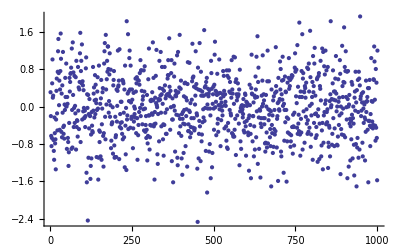

```mathematica
ListPlot[Zoom]
```

```mathematica
(*initial likelyhood logarithm*)
lnL=∑_(k=1)^ldata Log[prob/.{x->data[[k]],theta->Angoli[[k]] }]
```

-20127.3

```mathematica
(*NB: As a preliminar test, I checked the rho function for the coherent vacuum: the reconstructed function is consistent with rho=Diag(1,0,0,0) *)
```

```mathematica
For[i=1,i<11,i++,Print[lnL];Print[MatrixForm[rho]];
prob=∑_(b=0)^n ∑_(a=0)^n rho[[b+1,a+1]]Proj[[a+1,b+1]];lnL=0;R=0;
For[k1=1,k1<ldata+1,k1++,temp =prob/.{x->data[[k1]],theta->Angoli[[k1]] }; lnL=lnL+Log[temp];R=R+1/temp(Proj/.{x->data[[k1]],theta->Angoli[[k1]] })];temp2=R.rho.R;rho=temp2/Tr[temp2]]
```

-20127.3

(1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11)

-20127.3

(0.499683-4.07755×10^-19 ⅈ | 0.00229737+0.00364944 ⅈ | 0.0463808-0.0446229 ⅈ | -0.00328099-0.000891715 ⅈ | 0.00359641-0.00629771 ⅈ | -0.00151187+0.000408161 ⅈ | -0.00122554-0.00167435 ⅈ | 0.00177012-0.00177926 ⅈ | 0.0024461+0.000186381 ⅈ | -0.000296199+0.0000473461 ⅈ | -0.00141784-0.00240087 ⅈ
0.00229737-0.00364944 ⅈ | 0.149328-1.0149×10^-19 ⅈ | 0.00083262-0.000746783 ⅈ | 0.0179176-0.0192478 ⅈ | -0.00107589-0.000917766 ⅈ | 0.00157298+0.00173392 ⅈ | 0.00088848+0.000966588 ⅈ | -0.000913594+0.000202478 ⅈ | 0.000821948+0.000609126 ⅈ | 0.000036805+0.00150378 ⅈ | -0.00104971+0.00036955 ⅈ
0.0463808+0.0446229 ⅈ | 0.00083262+0.000746783 ⅈ | 0.0905093+4.03502×10^-19 ⅈ | 0.000655364+0.00072596 ⅈ | 0.0123394-0.0139025 ⅈ | -0.000352464-0.00130039 ⅈ | 0.000800926+0.000453336 ⅈ | 0.0000194909-0.000808269 ⅈ | 0.00122092+0.00103589 ⅈ | -0.000723604+0.00097047 ⅈ | 0.000274852-0.000166321 ⅈ
-0.00328099+0.000891715 ⅈ | 0.0179176+0.0192478 ⅈ | 0.000655364-0.00072596 ⅈ | 0.0604324+1.04599×10^-19 ⅈ | -0.000547655-0.000804082 ⅈ | 0.00754705-0.00944378 ⅈ | -0.000467314-0.000284455 ⅈ | 0.00160155+0.00139728 ⅈ | 0.00027116+0.000381601 ⅈ | -0.000853576-0.000702744 ⅈ | 0.000679949-0.000732557 ⅈ
0.00359641+0.00629771 ⅈ | -0.00107589+0.000917766 ⅈ | 0.0123394+0.0139025 ⅈ | -0.000547655+0.000804082 ⅈ | 0.0460527+1.28331×10^-21 ⅈ | -0.000156733+0.000477242 ⅈ | 0.00647575-0.00829313 ⅈ | 0.0000976119-0.000428249 ⅈ | 0.000302291+0.00189652 ⅈ | 0.000120551-0.0000581064 ⅈ | 0.000402127+0.000490398 ⅈ
-0.00151187-0.000408161 ⅈ | 0.00157298-0.00173392 ⅈ | -0.000352464+0.00130039 ⅈ | 0.00754705+0.00944378 ⅈ | -0.000156733-0.000477242 ⅈ | 0.0360457-2.11557×10^-22 ⅈ | 0.000386576-0.000232616 ⅈ | 0.00503236-0.00643002 ⅈ | -0.000386078-0.000219582 ⅈ | 0.00149666+0.00113561 ⅈ | 0.0000955426-0.000318768 ⅈ
-0.00122554+0.00167435 ⅈ | 0.00088848-0.000966588 ⅈ | 0.000800926-0.000453336 ⅈ | -0.000467314+0.000284455 ⅈ | 0.00647575+0.00829313 ⅈ | 0.000386576+0.000232616 ⅈ | 0.0307842-1.75893×10^-21 ⅈ | 0.0000609403+0.00011424 ⅈ | 0.00428258-0.00572477 ⅈ | 0.0000441656-0.000390319 ⅈ | 0.000357789+0.00185305 ⅈ
0.00177012+0.00177926 ⅈ | -0.000913594-0.000202478 ⅈ | 0.0000194909+0.000808269 ⅈ | 0.00160155-0.00139728 ⅈ | 0.0000976119+0.000428249 ⅈ | 0.00503236+0.00643002 ⅈ | 0.0000609403-0.00011424 ⅈ | 0.026316-1.42122×10^-22 ⅈ | -0.000365746-0.0000569434 ⅈ | 0.00393447-0.00507284 ⅈ | -0.000159092-0.0000562294 ⅈ
0.0024461-0.000186381 ⅈ | 0.000821948-0.000609126 ⅈ | 0.00122092-0.00103589 ⅈ | 0.00027116-0.000381601 ⅈ | 0.000302291-0.00189652 ⅈ | -0.000386078+0.000219582 ⅈ | 0.00428258+0.00572477 ⅈ | -0.000365746+0.0000569434 ⅈ | 0.0227262-1.33383×10^-22 ⅈ | 0.000423873+0.0000929752 ⅈ | 0.00316773-0.00459216 ⅈ
-0.000296199-0.0000473461 ⅈ | 0.000036805-0.00150378 ⅈ | -0.000723604-0.00097047 ⅈ | -0.000853576+0.000702744 ⅈ | 0.000120551+0.0000581064 ⅈ | 0.00149666-0.00113561 ⅈ | 0.0000441656+0.000390319 ⅈ | 0.00393447+0.00507284 ⅈ | 0.000423873-0.0000929752 ⅈ | 0.0207096-1.70868×10^-22 ⅈ | -0.000342484-0.0000702167 ⅈ
-0.00141784+0.00240087 ⅈ | -0.00104971-0.00036955 ⅈ | 0.000274852+0.000166321 ⅈ | 0.000679949+0.000732557 ⅈ | 0.000402127-0.000490398 ⅈ | 0.0000955426+0.000318768 ⅈ | 0.000357789-0.00185305 ⅈ | -0.000159092+0.0000562294 ⅈ | 0.00316773+0.00459216 ⅈ | -0.000342484+0.0000702167 ⅈ | 0.0174122+2.27752×10^-21 ⅈ)

-13789.3-2.68434×10^-15 ⅈ

(0.77392-4.59344×10^-19 ⅈ | 0.00432897+0.00600886 ⅈ | 0.0697296-0.06146 ⅈ | -0.00551913-0.000481461 ⅈ | 0.00395619-0.0135009 ⅈ | -0.00279564+0.00105349 ⅈ | -0.00284864-0.0030838 ⅈ | 0.00298952-0.00323178 ⅈ | 0.00420698+0.000751004 ⅈ | -0.0013182+0.00132538 ⅈ | -0.00194129-0.00263654 ⅈ
0.00432897-0.00600886 ⅈ | 0.121536-2.36996×10^-19 ⅈ | 0.00130355-0.00115467 ⅈ | 0.0163551-0.015745 ⅈ | -0.00118927-0.0010833 ⅈ | 0.000583836-0.000333729 ⅈ | 0.000590437+0.000760233 ⅈ | -0.000498086+0.000473047 ⅈ | 0.000405765+0.000977368 ⅈ | 0.0000844664+0.00115692 ⅈ | -0.000906992+0.000360035 ⅈ
0.0697296+0.06146 ⅈ | 0.00130355+0.00115467 ⅈ | 0.0493543+6.99049×10^-19 ⅈ | 0.000204427+0.000107189 ⅈ | 0.00766931-0.0079237 ⅈ | -0.000295185-0.0010474 ⅈ | 0.00013914-0.00113201 ⅈ | 0.000351171-0.000620421 ⅈ | 0.00093247+0.000964656 ⅈ | -0.00082505+0.000617203 ⅈ | 0.000137316-0.000317189 ⅈ
-0.00551913+0.000481461 ⅈ | 0.0163551+0.015745 ⅈ | 0.000204427-0.000107189 ⅈ | 0.0213596-1.01264×10^-20 ⅈ | -0.000632579-0.000590214 ⅈ | 0.00275808-0.00352575 ⅈ | -0.000111884-0.0000885946 ⅈ | 0.00033741+0.0000515809 ⅈ | 0.0000423749+0.000250135 ⅈ | -0.000390397-0.000276827 ⅈ | 0.000132697-0.0003614 ⅈ
0.00395619+0.0135009 ⅈ | -0.00118927+0.0010833 ⅈ | 0.00766931+0.0079237 ⅈ | -0.000632579+0.000590214 ⅈ | 0.0119676+8.36946×10^-21 ⅈ | -0.000112795+0.000099019 ⅈ | 0.00186683-0.00258115 ⅈ | 0.000147397-0.000100052 ⅈ | -0.0000123958+0.000450407 ⅈ | -0.0000754105-0.0000780284 ⅈ | 0.000231277+0.0000486098 ⅈ
-0.00279564-0.00105349 ⅈ | 0.000583836+0.000333729 ⅈ | -0.000295185+0.0010474 ⅈ | 0.00275808+0.00352575 ⅈ | -0.000112795-0.000099019 ⅈ | 0.00684551+2.04175×10^-20 ⅈ | 0.00021009-0.0000382987 ⅈ | 0.00109157-0.00146623 ⅈ | -0.000115477-0.0000599094 ⅈ | 0.000311435+9.41083×10^-6 ⅈ | 0.0000873451-0.000121015 ⅈ
-0.00284864+0.0030838 ⅈ | 0.000590437-0.000760233 ⅈ | 0.00013914+0.00113201 ⅈ | -0.000111884+0.0000885946 ⅈ | 0.00186683+0.00258115 ⅈ | 0.00021009+0.0000382987 ⅈ | 0.00500189+1.31808×10^-20 ⅈ | -1.15677×10^-6+0.0000348155 ⅈ | 0.000737076-0.00110347 ⅈ | 0.0000379509-0.000119328 ⅈ | 0.0000437363+0.00030691 ⅈ
0.00298952+0.00323178 ⅈ | -0.000498086-0.000473047 ⅈ | 0.000351171+0.000620421 ⅈ | 0.00033741-0.0000515809 ⅈ | 0.000147397+0.000100052 ⅈ | 0.00109157+0.00146623 ⅈ | -1.15677×10^-6-0.0000348155 ⅈ | 0.00357266-2.2404×10^-20 ⅈ | -0.000127659-9.4094×10^-7 ⅈ | 0.000600831-0.000881532 ⅈ | 0.0000184782-0.0000153714 ⅈ
0.00420698-0.000751004 ⅈ | 0.000405765-0.000977368 ⅈ | 0.00093247-0.000964656 ⅈ | 0.0000423749-0.000250135 ⅈ | -0.0000123958-0.000450407 ⅈ | -0.000115477+0.0000599094 ⅈ | 0.000737076+0.00110347 ⅈ | -0.000127659+9.4094×10^-7 ⅈ | 0.00274073+2.62825×10^-22 ⅈ | 0.000077099+0.0000300759 ⅈ | 0.000371491-0.00072159 ⅈ
-0.0013182-0.00132538 ⅈ | 0.0000844664-0.00115692 ⅈ | -0.00082505-0.000617203 ⅈ | -0.000390397+0.000276827 ⅈ | -0.0000754105+0.0000780284 ⅈ | 0.000311435-9.41083×10^-6 ⅈ | 0.0000379509+0.000119328 ⅈ | 0.000600831+0.000881532 ⅈ | 0.000077099-0.0000300759 ⅈ | 0.00212292-1.02551×10^-20 ⅈ | -0.0000475148+7.83847×10^-6 ⅈ
-0.00194129+0.00263654 ⅈ | -0.000906992-0.000360035 ⅈ | 0.000137316+0.000317189 ⅈ | 0.000132697+0.0003614 ⅈ | 0.000231277-0.0000486098 ⅈ | 0.0000873451+0.000121015 ⅈ | 0.0000437363-0.00030691 ⅈ | 0.0000184782+0.0000153714 ⅈ | 0.000371491+0.00072159 ⅈ | -0.0000475148-7.83847×10^-6 ⅈ | 0.00157957-2.15407×10^-21 ⅈ)

-12068.1+4.20383×10^-15 ⅈ

(0.839758-4.32654×10^-20 ⅈ | 0.00544934+0.00643529 ⅈ | 0.0810728-0.0638376 ⅈ | -0.00774324+0.00072977 ⅈ | 0.00448309-0.0158334 ⅈ | -0.00416263+0.00177592 ⅈ | -0.0042707-0.00349894 ⅈ | 0.00335764-0.00355589 ⅈ | 0.00467297+0.0011967 ⅈ | -0.00250753+0.00279479 ⅈ | -0.00182422-0.00216925 ⅈ
0.00544934-0.00643529 ⅈ | 0.101478-1.5692×10^-19 ⅈ | 0.0014806-0.0013577 ⅈ | 0.0151592-0.0121686 ⅈ | -0.00123121-0.00122176 ⅈ | 0.000173664-0.00102743 ⅈ | 0.000154133+0.000572616 ⅈ | -0.000430061+0.000858963 ⅈ | -0.000166574+0.00127928 ⅈ | 0.000043294+0.00102519 ⅈ | -0.000770595+0.000305573 ⅈ
0.0810728+0.0638376 ⅈ | 0.0014806+0.0013577 ⅈ | 0.0368718+2.0101×10^-19 ⅈ | -0.000505402-0.000146907 ⅈ | 0.00604077-0.00528912 ⅈ | -0.000396533-0.000911446 ⅈ | -0.000059357-0.00169246 ⅈ | 0.000447502-0.000446309 ⅈ | 0.000509196+0.000831856 ⅈ | -0.00104272+0.000443381 ⅈ | 0.0000351487-0.000275989 ⅈ
-0.00774324-0.00072977 ⅈ | 0.0151592+0.0121686 ⅈ | -0.000505402+0.000146907 ⅈ | 0.0118571+1.15726×10^-20 ⅈ | -0.000739461-0.000433913 ⅈ | 0.00153999-0.00173627 ⅈ | -0.0000186662+0.0000143126 ⅈ | 0.0000241692-0.000235165 ⅈ | -0.00012491+0.000209691 ⅈ | -0.000341888-0.000209715 ⅈ | -1.38692×10^-6-0.000205862 ⅈ
0.00448309+0.0158334 ⅈ | -0.00123121+0.00122176 ⅈ | 0.00604077+0.00528912 ⅈ | -0.000739461+0.000433913 ⅈ | 0.00504794-1.4774×10^-19 ⅈ | -0.0000876777-0.0000132992 ⅈ | 0.000845915-0.00113405 ⅈ | 0.0000810486+0.0000105787 ⅈ | -0.000018737+0.0000569709 ⅈ | -0.000121088-0.0000946171 ⅈ | 0.0000780581-0.0000976771 ⅈ
-0.00416263-0.00177592 ⅈ | 0.000173664+0.00102743 ⅈ | -0.000396533+0.000911446 ⅈ | 0.00153999+0.00173627 ⅈ | -0.0000876777+0.0000132992 ⅈ | 0.00197984+7.20014×10^-20 ⅈ | 0.000128123+0.0000397103 ⅈ | 0.000379532-0.000435932 ⅈ | -0.0000961875-0.0000139241 ⅈ | 0.0000791462-0.000187968 ⅈ | 0.0000797992-0.0000421375 ⅈ
-0.0042707+0.00349894 ⅈ | 0.000154133-0.000572616 ⅈ | -0.000059357+0.00169246 ⅈ | -0.0000186662-0.0000143126 ⅈ | 0.000845915+0.00113405 ⅈ | 0.000128123-0.0000397103 ⅈ | 0.00121444+6.50589×10^-20 ⅈ | -0.0000144718+0.0000392384 ⅈ | 0.00018399-0.000241781 ⅈ | 0.0000150662-0.0000764746 ⅈ | 0.0000367898-8.75983×10^-6 ⅈ
0.00335764+0.00355589 ⅈ | -0.000430061-0.000858963 ⅈ | 0.000447502+0.000446309 ⅈ | 0.0000241692+0.000235165 ⅈ | 0.0000810486-0.0000105787 ⅈ | 0.000379532+0.000435932 ⅈ | -0.0000144718-0.0000392384 ⅈ | 0.000736889+1.20899×10^-20 ⅈ | -0.0000573882+9.54434×10^-6 ⅈ | 0.000124895-0.000208486 ⅈ | 0.000030612+3.63679×10^-6 ⅈ
0.00467297-0.0011967 ⅈ | -0.000166574-0.00127928 ⅈ | 0.000509196-0.000831856 ⅈ | -0.00012491-0.000209691 ⅈ | -0.000018737-0.0000569709 ⅈ | -0.0000961875+0.0000139241 ⅈ | 0.00018399+0.000241781 ⅈ | -0.0000573882-9.54434×10^-6 ⅈ | 0.000497985+4.65699×10^-21 ⅈ | 6.93176×10^-6+0.0000269722 ⅈ | 0.0000612903-0.000143348 ⅈ
-0.00250753-0.00279479 ⅈ | 0.000043294-0.00102519 ⅈ | -0.00104272-0.000443381 ⅈ | -0.000341888+0.000209715 ⅈ | -0.000121088+0.0000946171 ⅈ | 0.0000791462+0.000187968 ⅈ | 0.0000150662+0.0000764746 ⅈ | 0.000124895+0.000208486 ⅈ | 6.93176×10^-6-0.0000269722 ⅈ | 0.000344485-1.09313×10^-20 ⅈ | 7.83588×10^-6+0.0000279114 ⅈ
-0.00182422+0.00216925 ⅈ | -0.000770595-0.000305573 ⅈ | 0.0000351487+0.000275989 ⅈ | -1.38692×10^-6+0.000205862 ⅈ | 0.0000780581+0.0000976771 ⅈ | 0.0000797992+0.0000421375 ⅈ | 0.0000367898+8.75983×10^-6 ⅈ | 0.000030612-3.63679×10^-6 ⅈ | 0.0000612903+0.000143348 ⅈ | 7.83588×10^-6-0.0000279114 ⅈ | 0.000213854-7.53266×10^-21 ⅈ)

-11879.9-3.68747×10^-15 ⅈ

(0.859223-1.43229×10^-18 ⅈ | 0.00615162+0.00661755 ⅈ | 0.0876871-0.0649286 ⅈ | -0.00951601+0.00202903 ⅈ | 0.00477422-0.0152106 ⅈ | -0.00606419+0.00205278 ⅈ | -0.00462471-0.00300066 ⅈ | 0.00295826-0.00376303 ⅈ | 0.00509597+0.00183341 ⅈ | -0.0034203+0.00366493 ⅈ | -0.00198145-0.00200472 ⅈ
0.00615162-0.00661755 ⅈ | 0.0921682+1.02358×10^-19 ⅈ | 0.00155015-0.00155095 ⅈ | 0.0148515-0.0102542 ⅈ | -0.00105479-0.0013345 ⅈ | -0.0000653679-0.000601086 ⅈ | -0.000297901+0.000499627 ⅈ | -0.00038185+0.0014705 ⅈ | -0.000688875+0.00138861 ⅈ | 0.000118143+0.00114573 ⅈ | -0.000722998+0.000332839 ⅈ
0.0876871+0.0649286 ⅈ | 0.00155015+0.00155095 ⅈ | 0.0335447+9.22397×10^-19 ⅈ | -0.00110429-0.000215183 ⅈ | 0.00544089-0.00414445 ⅈ | -0.000486093-0.000942373 ⅈ | -0.0000835657-0.0016391 ⅈ | 0.000378079-0.000443833 ⅈ | 0.000275563+0.000891468 ⅈ | -0.0012579+0.000342055 ⅈ | 0.0000101914-0.000245586 ⅈ
-0.00951601-0.00202903 ⅈ | 0.0148515+0.0102542 ⅈ | -0.00110429+0.000215183 ⅈ | 0.00940755+4.84471×10^-19 ⅈ | -0.000837354-0.000377399 ⅈ | 0.00114912-0.00110382 ⅈ | -0.0000236325+0.0000670797 ⅈ | -0.0000372175-0.0000999872 ⅈ | -0.000228192+0.000154791 ⅈ | -0.000345236-0.000176285 ⅈ | -3.01783×10^-6-0.000152117 ⅈ
0.00477422+0.0152106 ⅈ | -0.00105479+0.0013345 ⅈ | 0.00544089+0.00414445 ⅈ | -0.000837354+0.000377399 ⅈ | 0.00335727-1.65589×10^-19 ⅈ | -0.0000676777-0.000037439 ⅈ | 0.000592338-0.000707728 ⅈ | 1.91725×10^-6+0.0000159398 ⅈ | -0.0000148349+7.94488×10^-6 ⅈ | -0.000122548-0.000114974 ⅈ | 0.0000257054-0.000109442 ⅈ
-0.00606419-0.00205278 ⅈ | -0.0000653679+0.000601086 ⅈ | -0.000486093+0.000942373 ⅈ | 0.00114912+0.00110382 ⅈ | -0.0000676777+0.000037439 ⅈ | 0.0010168+3.50007×10^-20 ⅈ | 0.000101336+0.0000665287 ⅈ | 0.000229957-0.000179077 ⅈ | -0.0000993038-0.0000207215 ⅈ | 0.0000468959-0.000210788 ⅈ | 0.0000893115-5.56627×10^-6 ⅈ
-0.00462471+0.00300066 ⅈ | -0.000297901-0.000499627 ⅈ | -0.0000835657+0.0016391 ⅈ | -0.0000236325-0.0000670797 ⅈ | 0.000592338+0.000707728 ⅈ | 0.000101336-0.0000665287 ⅈ | 0.000533794+5.61005×10^-20 ⅈ | -0.0000247696+0.0000200194 ⅈ | 0.0000790748-0.0000757912 ⅈ | 0.0000104884-0.0000822842 ⅈ | 0.0000439274-0.0000481915 ⅈ
0.00295826+0.00376303 ⅈ | -0.00038185-0.0014705 ⅈ | 0.000378079+0.000443833 ⅈ | -0.0000372175+0.0000999872 ⅈ | 1.91725×10^-6-0.0000159398 ⅈ | 0.000229957+0.000179077 ⅈ | -0.0000247696-0.0000200194 ⅈ | 0.000309727+2.17442×10^-20 ⅈ | -0.0000264057+0.0000214854 ⅈ | 0.000051086-0.000102125 ⅈ | 0.0000295763+0.0000120098 ⅈ
0.00509597-0.00183341 ⅈ | -0.000688875-0.00138861 ⅈ | 0.000275563-0.000891468 ⅈ | -0.000228192-0.000154791 ⅈ | -0.0000148349-7.94488×10^-6 ⅈ | -0.0000993038+0.0000207215 ⅈ | 0.0000790748+0.0000757912 ⅈ | -0.0000264057-0.0000214854 ⅈ | 0.000200713+1.51727×10^-20 ⅈ | 1.408×10^-6+0.0000276801 ⅈ | 0.0000233451-0.0000486312 ⅈ
-0.0034203-0.00366493 ⅈ | 0.000118143-0.00114573 ⅈ | -0.0012579-0.000342055 ⅈ | -0.000345236+0.000176285 ⅈ | -0.000122548+0.000114974 ⅈ | 0.0000468959+0.000210788 ⅈ | 0.0000104884+0.0000822842 ⅈ | 0.000051086+0.000102125 ⅈ | 1.408×10^-6-0.0000276801 ⅈ | 0.000166743-4.06914×10^-20 ⅈ | 0.0000147835+0.0000382987 ⅈ
-0.00198145+0.00200472 ⅈ | -0.000722998-0.000332839 ⅈ | 0.0000101914+0.000245586 ⅈ | -3.01783×10^-6+0.000152117 ⅈ | 0.0000257054+0.000109442 ⅈ | 0.0000893115+5.56627×10^-6 ⅈ | 0.0000439274+0.0000481915 ⅈ | 0.0000295763-0.0000120098 ⅈ | 0.0000233451+0.0000486312 ⅈ | 0.0000147835-0.0000382987 ⅈ | 0.0000711398+1.33088×10^-21 ⅈ)

-11853.7-3.82321×10^-15 ⅈ

(0.867156-8.58972×10^-19 ⅈ | 0.00673464+0.00671306 ⅈ | 0.0911673-0.0663526 ⅈ | -0.0105447+0.00324793 ⅈ | 0.00466655-0.0141703 ⅈ | -0.00782563+0.00222628 ⅈ | -0.00470468-0.00244385 ⅈ | 0.0022665-0.0040783 ⅈ | 0.00552632+0.00257628 ⅈ | -0.00399922+0.0041648 ⅈ | -0.00212104-0.00188388 ⅈ
0.00673464-0.00671306 ⅈ | 0.0873526-2.43021×10^-19 ⅈ | 0.0016414-0.0017168 ⅈ | 0.014702-0.00921256 ⅈ | -0.000758811-0.00141309 ⅈ | -0.000335173+0.0000478656 ⅈ | -0.000693243+0.000424728 ⅈ | -0.000295155+0.00206855 ⅈ | -0.00105731+0.00134834 ⅈ | 0.000254316+0.00133658 ⅈ | -0.000724826+0.000420661 ⅈ
0.0911673+0.0663526 ⅈ | 0.0016414+0.0017168 ⅈ | 0.0325454+7.61013×10^-19 ⅈ | -0.00154456-0.000198167 ⅈ | 0.00511515-0.00357252 ⅈ | -0.000532702-0.00102583 ⅈ | -0.0000954369-0.0014809 ⅈ | 0.000284215-0.000551319 ⅈ | 0.000129541+0.00102689 ⅈ | -0.00139876+0.000264697 ⅈ | 0.0000235304-0.000211577 ⅈ
-0.0105447-0.00324793 ⅈ | 0.014702+0.00921256 ⅈ | -0.00154456+0.000198167 ⅈ | 0.00855234+2.96493×10^-19 ⅈ | -0.000914156-0.000356163 ⅈ | 0.000942218-0.000798811 ⅈ | -0.0000420263+0.0000861927 ⅈ | -0.0000643498+0.0000944675 ⅈ | -0.00028001+0.0000778611 ⅈ | -0.000346895-0.00012838 ⅈ | 4.79692×10^-6-0.000136116 ⅈ
0.00466655+0.0141703 ⅈ | -0.000758811+0.00141309 ⅈ | 0.00511515+0.00357252 ⅈ | -0.000914156+0.000356163 ⅈ | 0.00271485-5.43134×10^-21 ⅈ | -0.0000537547-0.0000334235 ⅈ | 0.000484283-0.000526359 ⅈ | -0.000053243-6.13172×10^-6 ⅈ | -0.0000300788+0.0000232203 ⅈ | -0.000115908-0.000126992 ⅈ | 5.90464×10^-6-0.000086848 ⅈ
-0.00782563-0.00222628 ⅈ | -0.000335173-0.0000478656 ⅈ | -0.000532702+0.00102583 ⅈ | 0.000942218+0.000798811 ⅈ | -0.0000537547+0.0000334235 ⅈ | 0.000742614+1.91801×10^-20 ⅈ | 0.0000938949+0.0000804507 ⅈ | 0.000180319-0.0000879858 ⅈ | -0.0000949141-0.0000315196 ⅈ | 0.0000427636-0.000217981 ⅈ | 0.00010161+0.0000154491 ⅈ
-0.00470468+0.00244385 ⅈ | -0.000693243-0.000424728 ⅈ | -0.0000954369+0.0014809 ⅈ | -0.0000420263-0.0000861927 ⅈ | 0.000484283+0.000526359 ⅈ | 0.0000938949-0.0000804507 ⅈ | 0.000341622+2.56532×10^-20 ⅈ | -0.0000263477-7.37128×10^-6 ⅈ | 0.0000446918-0.0000376442 ⅈ | 7.64969×10^-6-0.0000902613 ⅈ | 0.0000437951-0.0000482779 ⅈ
0.0022665+0.0040783 ⅈ | -0.000295155-0.00206855 ⅈ | 0.000284215+0.000551319 ⅈ | -0.0000643498-0.0000944675 ⅈ | -0.000053243+6.13172×10^-6 ⅈ | 0.000180319+0.0000879858 ⅈ | -0.0000263477+7.37128×10^-6 ⅈ | 0.000225714-3.97413×10^-21 ⅈ | -9.0838×10^-6+0.0000392641 ⅈ | 0.0000355267-0.0000868096 ⅈ | 0.0000325956+0.0000182978 ⅈ
0.00552632-0.00257628 ⅈ | -0.00105731-0.00134834 ⅈ | 0.000129541-0.00102689 ⅈ | -0.00028001-0.0000778611 ⅈ | -0.0000300788-0.0000232203 ⅈ | -0.0000949141+0.0000315196 ⅈ | 0.0000446918+0.0000376442 ⅈ | -9.0838×10^-6-0.0000392641 ⅈ | 0.000154778+2.19595×10^-20 ⅈ | 5.83242×10^-6+0.0000267744 ⅈ | 0.0000129346-0.0000309341 ⅈ
-0.00399922-0.0041648 ⅈ | 0.000254316-0.00133658 ⅈ | -0.00139876-0.000264697 ⅈ | -0.000346895+0.00012838 ⅈ | -0.000115908+0.000126992 ⅈ | 0.0000427636+0.000217981 ⅈ | 7.64969×10^-6+0.0000902613 ⅈ | 0.0000355267+0.0000868096 ⅈ | 5.83242×10^-6-0.0000267744 ⅈ | 0.000160017-1.49761×10^-20 ⅈ | 0.0000136638+0.0000471353 ⅈ
-0.00212104+0.00188388 ⅈ | -0.000724826-0.000420661 ⅈ | 0.0000235304+0.000211577 ⅈ | 4.79692×10^-6+0.000136116 ⅈ | 5.90464×10^-6+0.000086848 ⅈ | 0.00010161-0.0000154491 ⅈ | 0.0000437951+0.0000482779 ⅈ | 0.0000325956-0.0000182978 ⅈ | 0.0000129346+0.0000309341 ⅈ | 0.0000136638-0.0000471353 ⅈ | 0.0000541379+2.07478×10^-21 ⅈ)

-11847.5+2.47817×10^-16 ⅈ

(0.871114-8.86099×10^-19 ⅈ | 0.00714383+0.00676502 ⅈ | 0.0930179-0.067732 ⅈ | -0.0111578+0.00420715 ⅈ | 0.00454516-0.0134426 ⅈ | -0.00901405+0.00233914 ⅈ | -0.00475225-0.00206246 ⅈ | 0.0017687-0.00427913 ⅈ | 0.00578088+0.00315327 ⅈ | -0.00425024+0.00445372 ⅈ | -0.00212903-0.00175663 ⅈ
0.00714383-0.00676502 ⅈ | 0.0845947-4.12987×10^-19 ⅈ | 0.00174072-0.00183283 ⅈ | 0.0145768-0.00856978 ⅈ | -0.000495543-0.00151248 ⅈ | -0.000580496+0.000625422 ⅈ | -0.000968962+0.000322032 ⅈ | -0.000196214+0.00251579 ⅈ | -0.00126395+0.00125775 ⅈ | 0.000371561+0.0014811 ⅈ | -0.000736278+0.000511326 ⅈ
0.0930179+0.067732 ⅈ | 0.00174072+0.00183283 ⅈ | 0.032253+3.95252×10^-19 ⅈ | -0.0018668-0.000162052 ⅈ | 0.00493306-0.00326176 ⅈ | -0.000530203-0.00111361 ⅈ | -0.000115959-0.00135145 ⅈ | 0.000236798-0.000652571 ⅈ | 0.0000167254+0.00113353 ⅈ | -0.00145893+0.000219657 ⅈ | 0.0000538447-0.000180874 ⅈ
-0.0111578-0.00420715 ⅈ | 0.0145768+0.00856978 ⅈ | -0.0018668+0.000162052 ⅈ | 0.00816199+7.0876×10^-19 ⅈ | -0.000972115-0.000361095 ⅈ | 0.0008052-0.000620208 ⅈ | -0.0000508494+0.0000846447 ⅈ | -0.0000867722+0.000249435 ⅈ | -0.000294033+0.0000128617 ⅈ | -0.000344353-0.0000906572 ⅈ | 4.56706×10^-6-0.000131133 ⅈ
0.00454516+0.0134426 ⅈ | -0.000495543+0.00151248 ⅈ | 0.00493306+0.00326176 ⅈ | -0.000972115+0.000361095 ⅈ | 0.00238386+1.93866×10^-19 ⅈ | -0.0000401795-0.000024592 ⅈ | 0.000413468-0.00043028 ⅈ | -0.000081197-0.0000246043 ⅈ | -0.000053917+0.0000402536 ⅈ | -0.000108492-0.000125612 ⅈ | 1.30509×10^-8-0.0000610883 ⅈ
-0.00901405-0.00233914 ⅈ | -0.000580496-0.000625422 ⅈ | -0.000530203+0.00111361 ⅈ | 0.0008052+0.000620208 ⅈ | -0.0000401795+0.000024592 ⅈ | 0.000646225+3.75714×10^-21 ⅈ | 0.0000964789+0.0000883572 ⅈ | 0.000159959-0.0000544399 ⅈ | -0.0000855583-0.0000360398 ⅈ | 0.0000413957-0.000225639 ⅈ | 0.000110273+0.0000280637 ⅈ
-0.00475225+0.00206246 ⅈ | -0.000968962-0.000322032 ⅈ | -0.000115959+0.00135145 ⅈ | -0.0000508494-0.0000846447 ⅈ | 0.000413468+0.00043028 ⅈ | 0.0000964789-0.0000883572 ⅈ | 0.000263416+4.16055×10^-20 ⅈ | -0.0000235887-0.0000298206 ⅈ | 0.0000286349-0.0000301536 ⅈ | 3.06995×10^-6-0.0000947026 ⅈ | 0.0000419282-0.0000439188 ⅈ
0.0017687+0.00427913 ⅈ | -0.000196214-0.00251579 ⅈ | 0.000236798+0.000652571 ⅈ | -0.0000867722-0.000249435 ⅈ | -0.000081197+0.0000246043 ⅈ | 0.000159959+0.0000544399 ⅈ | -0.0000235887+0.0000298206 ⅈ | 0.000210132-2.88877×10^-20 ⅈ | 7.64521×10^-7+0.0000548463 ⅈ | 0.0000332382-0.0000865462 ⅈ | 0.0000360666+0.0000229779 ⅈ
0.00578088-0.00315327 ⅈ | -0.00126395-0.00125775 ⅈ | 0.0000167254-0.00113353 ⅈ | -0.000294033-0.0000128617 ⅈ | -0.000053917-0.0000402536 ⅈ | -0.0000855583+0.0000360398 ⅈ | 0.0000286349+0.0000301536 ⅈ | 7.64521×10^-7-0.0000548463 ⅈ | 0.000149082-4.68545×10^-21 ⅈ | 9.72087×10^-6+0.0000238999 ⅈ | 9.21823×10^-6-0.0000287855 ⅈ
-0.00425024-0.00445372 ⅈ | 0.000371561-0.0014811 ⅈ | -0.00145893-0.000219657 ⅈ | -0.000344353+0.0000906572 ⅈ | -0.000108492+0.000125612 ⅈ | 0.0000413957+0.000225639 ⅈ | 3.06995×10^-6+0.0000947026 ⅈ | 0.0000332382+0.0000865462 ⅈ | 9.72087×10^-6-0.0000238999 ⅈ | 0.000170113-1.46112×10^-20 ⅈ | 0.0000111573+0.000053545 ⅈ
-0.00212903+0.00175663 ⅈ | -0.000736278-0.000511326 ⅈ | 0.0000538447+0.000180874 ⅈ | 4.56706×10^-6+0.000131133 ⅈ | 1.30509×10^-8+0.0000610883 ⅈ | 0.000110273-0.0000280637 ⅈ | 0.0000419282+0.0000439188 ⅈ | 0.0000360666-0.0000229779 ⅈ | 9.21823×10^-6+0.0000287855 ⅈ | 0.0000111573-0.000053545 ⅈ | 0.0000530993+4.03038×10^-21 ⅈ)

-11845.4-1.12171×10^-16 ⅈ

(0.87333-1.15375×10^-18 ⅈ | 0.0073985+0.00679759 ⅈ | 0.0940819-0.0688301 ⅈ | -0.0115573+0.0049111 ⅈ | 0.00449605-0.0130694 ⅈ | -0.00970285+0.00244696 ⅈ | -0.00481377-0.00184222 ⅈ | 0.00149453-0.00434746 ⅈ | 0.00588117+0.00350591 ⅈ | -0.00431888+0.00462003 ⅈ | -0.0020916-0.00165954 ⅈ
0.0073985-0.00679759 ⅈ | 0.0829068-9.41932×10^-19 ⅈ | 0.00184905-0.0019059 ⅈ | 0.014467-0.00811071 ⅈ | -0.00030085-0.00163483 ⅈ | -0.000764786+0.00108581 ⅈ | -0.001151+0.000221517 ⅈ | -0.000115012+0.00282318 ⅈ | -0.00136709+0.00116459 ⅈ | 0.000451529+0.00156601 ⅈ | -0.000743232+0.000589175 ⅈ
0.0940819+0.0688301 ⅈ | 0.00184905+0.0019059 ⅈ | 0.0322188+1.0838×10^-18 ⅈ | -0.0021012-0.000125697 ⅈ | 0.00484532-0.00308708 ⅈ | -0.00050228-0.00118001 ⅈ | -0.000136316-0.00126603 ⅈ | 0.000226946-0.000717859 ⅈ | -0.0000735462+0.00119751 ⅈ | -0.00147251+0.000198257 ⅈ | 0.000081495-0.00016171 ⅈ
-0.0115573-0.0049111 ⅈ | 0.014467+0.00811071 ⅈ | -0.0021012+0.000125697 ⅈ | 0.00794221+9.54301×10^-19 ⅈ | -0.00101366-0.000382562 ⅈ | 0.000711499-0.000502708 ⅈ | -0.0000561788+0.0000753052 ⅈ | -0.000104871+0.000355362 ⅈ | -0.000289605-0.0000319563 ⅈ | -0.000338865-0.0000676683 ⅈ | 2.45249×10^-8-0.000125568 ⅈ
0.00449605+0.0130694 ⅈ | -0.00030085+0.00163483 ⅈ | 0.00484532+0.00308708 ⅈ | -0.00101366+0.000382562 ⅈ | 0.00218126+1.08873×10^-19 ⅈ | -0.0000281024-0.0000176579 ⅈ | 0.000360803-0.000372476 ⅈ | -0.0000923265-0.0000359534 ⅈ | -0.0000783831+0.0000514901 ⅈ | -0.000103543-0.00011791 ⅈ | -5.45724×10^-8-0.0000406098 ⅈ
-0.00970285-0.00244696 ⅈ | -0.000764786-0.00108581 ⅈ | -0.00050228+0.00118001 ⅈ | 0.000711499+0.000502708 ⅈ | -0.0000281024+0.0000176579 ⅈ | 0.00060958-4.7224×10^-20 ⅈ | 0.000102265+0.0000931491 ⅈ | 0.000152121-0.0000444188 ⅈ | -0.0000757441-0.0000361024 ⅈ | 0.0000402636-0.000232321 ⅈ | 0.000115635+0.0000355994 ⅈ
-0.00481377+0.00184222 ⅈ | -0.001151-0.000221517 ⅈ | -0.000136316+0.00126603 ⅈ | -0.0000561788-0.0000753052 ⅈ | 0.000360803+0.000372476 ⅈ | 0.000102265-0.0000931491 ⅈ | 0.000222995+1.11049×10^-20 ⅈ | -0.0000205994-0.0000448148 ⅈ | 0.0000192522-0.0000309484 ⅈ | -1.81664×10^-6-0.0000966078 ⅈ | 0.0000403502-0.0000399972 ⅈ
0.00149453+0.00434746 ⅈ | -0.000115012-0.00282318 ⅈ | 0.000226946+0.000717859 ⅈ | -0.000104871-0.000355362 ⅈ | -0.0000923265+0.0000359534 ⅈ | 0.000152121+0.0000444188 ⅈ | -0.0000205994+0.0000448148 ⅈ | 0.000210015+4.57535×10^-21 ⅈ | 6.2697×10^-6+0.0000657538 ⅈ | 0.0000343867-0.0000874322 ⅈ | 0.0000388434+0.0000264874 ⅈ
0.00588117-0.00350591 ⅈ | -0.00136709-0.00116459 ⅈ | -0.0000735462-0.00119751 ⅈ | -0.000289605+0.0000319563 ⅈ | -0.0000783831-0.0000514901 ⅈ | -0.0000757441+0.0000361024 ⅈ | 0.0000192522+0.0000309484 ⅈ | 6.2697×10^-6-0.0000657538 ⅈ | 0.000148565-2.92264×10^-21 ⅈ | 0.0000119353+0.0000206751 ⅈ | 7.95911×10^-6-0.0000297732 ⅈ
-0.00431888-0.00462003 ⅈ | 0.000451529-0.00156601 ⅈ | -0.00147251-0.000198257 ⅈ | -0.000338865+0.0000676683 ⅈ | -0.000103543+0.00011791 ⅈ | 0.0000402636+0.000232321 ⅈ | -1.81664×10^-6+0.0000966078 ⅈ | 0.0000343867+0.0000874322 ⅈ | 0.0000119353-0.0000206751 ⅈ | 0.000176763-3.32054×10^-20 ⅈ | 9.18804×10^-6+0.0000578147 ⅈ
-0.0020916+0.00165954 ⅈ | -0.000743232-0.000589175 ⅈ | 0.000081495+0.00016171 ⅈ | 2.45249×10^-8+0.000125568 ⅈ | -5.45724×10^-8+0.0000406098 ⅈ | 0.000115635-0.0000355994 ⅈ | 0.0000403502+0.0000399972 ⅈ | 0.0000388434-0.0000264874 ⅈ | 7.95911×10^-6+0.0000297732 ⅈ | 9.18804×10^-6-0.0000578147 ⅈ | 0.000053317+1.63837×10^-20 ⅈ)

-11844.5+1.05991×10^-15 ⅈ

(0.874651+6.53215×10^-19 ⅈ | 0.00753328+0.00681692 ⅈ | 0.0947376-0.0696518 ⅈ | -0.0118271+0.00542217 ⅈ | 0.00448574-0.0129322 ⅈ | -0.010079+0.00256654 ⅈ | -0.00488215-0.00172458 ⅈ | 0.00135442-0.00434435 ⅈ | 0.00590603+0.00370197 ⅈ | -0.0043174+0.00471502 ⅈ | -0.00205905-0.00159321 ⅈ
0.00753328-0.00681692 ⅈ | 0.0818227-2.58323×10^-19 ⅈ | 0.00196447-0.00194848 ⅈ | 0.0143705-0.00775213 ⅈ | -0.000163614-0.00176593 ⅈ | -0.000891682+0.0014474 ⅈ | -0.00127633+0.000135341 ⅈ | -0.0000563314+0.00303801 ⅈ | -0.00141701+0.00108184 ⅈ | 0.000503521+0.00161334 ⅈ | -0.000746223+0.000653512 ⅈ
0.0947376+0.0696518 ⅈ | 0.00196447+0.00194848 ⅈ | 0.0322932-3.66413×10^-19 ⅈ | -0.00227185-0.0000902756 ⅈ | 0.00481366-0.00299201 ⅈ | -0.000467-0.00122239 ⅈ | -0.000152811-0.00121368 ⅈ | 0.000235821-0.000755754 ⅈ | -0.000144559+0.00123488 ⅈ | -0.00146663+0.000188181 ⅈ | 0.000100692-0.00015147 ⅈ
-0.0118271-0.00542217 ⅈ | 0.0143705+0.00775213 ⅈ | -0.00227185+0.0000902756 ⅈ | 0.00779904+7.01318×10^-20 ⅈ | -0.0010431-0.000411713 ⅈ | 0.000647072-0.000420902 ⅈ | -0.0000625427+0.0000638036 ⅈ | -0.000118394+0.000425584 ⅈ | -0.000279119-0.0000615383 ⅈ | -0.000332441-0.0000541692 ⅈ | -5.29974×10^-6-0.000118198 ⅈ
0.00448574+0.0129322 ⅈ | -0.000163614+0.00176593 ⅈ | 0.00481366+0.00299201 ⅈ | -0.0010431+0.000411713 ⅈ | 0.00204448-4.49703×10^-20 ⅈ | -0.0000183152-0.0000126602 ⅈ | 0.000320525-0.000335171 ⅈ | -0.0000947722-0.0000425457 ⅈ | -0.00010079+0.0000589332 ⅈ | -0.000101155-0.000109371 ⅈ | 1.3111×10^-6-0.000025297 ⅈ
-0.010079-0.00256654 ⅈ | -0.000891682-0.0014474 ⅈ | -0.000467+0.00122239 ⅈ | 0.000647072+0.000420902 ⅈ | -0.0000183152+0.0000126602 ⅈ | 0.000597086-8.02446×10^-20 ⅈ | 0.000108035+0.0000964537 ⅈ | 0.000150771-0.00004351 ⅈ | -0.000067718-0.0000342198 ⅈ | 0.0000397479-0.000237385 ⅈ | 0.000119321+0.0000402761 ⅈ
-0.00488215+0.00172458 ⅈ | -0.00127633-0.000135341 ⅈ | -0.000152811+0.00121368 ⅈ | -0.0000625427-0.0000638036 ⅈ | 0.000320525+0.000335171 ⅈ | 0.000108035-0.0000964537 ⅈ | 0.000198675-1.89804×10^-20 ⅈ | -0.0000182932-0.0000543144 ⅈ | 0.0000126484-0.0000336487 ⅈ | -5.99192×10^-6-0.0000972641 ⅈ | 0.0000391632-0.0000369648 ⅈ
0.00135442+0.00434435 ⅈ | -0.0000563314-0.00303801 ⅈ | 0.000235821+0.000755754 ⅈ | -0.000118394-0.000425584 ⅈ | -0.0000947722+0.0000425457 ⅈ | 0.000150771+0.00004351 ⅈ | -0.0000182932+0.0000543144 ⅈ | 0.000213545+5.09609×10^-20 ⅈ | 9.28984×10^-6+0.0000728652 ⅈ | 0.0000362829-0.0000878286 ⅈ | 0.0000412045+0.0000291158 ⅈ
0.00590603-0.00370197 ⅈ | -0.00141701-0.00108184 ⅈ | -0.000144559-0.00123488 ⅈ | -0.000279119+0.0000615383 ⅈ | -0.00010079-0.0000589332 ⅈ | -0.000067718+0.0000342198 ⅈ | 0.0000126484+0.0000336487 ⅈ | 9.28984×10^-6-0.0000728652 ⅈ | 0.000147902+1.77363×10^-20 ⅈ | 0.0000129145+0.0000180863 ⅈ | 7.39722×10^-6-0.0000310521 ⅈ
-0.0043174-0.00471502 ⅈ | 0.000503521-0.00161334 ⅈ | -0.00146663-0.000188181 ⅈ | -0.000332441+0.0000541692 ⅈ | -0.000101155+0.000109371 ⅈ | 0.0000397479+0.000237385 ⅈ | -5.99192×10^-6+0.0000972641 ⅈ | 0.0000362829+0.0000878286 ⅈ | 0.0000129145-0.0000180863 ⅈ | 0.000179662-1.78767×10^-20 ⅈ | 7.9928×10^-6+0.0000607031 ⅈ
-0.00205905+0.00159321 ⅈ | -0.000746223-0.000653512 ⅈ | 0.000100692+0.00015147 ⅈ | -5.29974×10^-6+0.000118198 ⅈ | 1.3111×10^-6+0.000025297 ⅈ | 0.000119321-0.0000402761 ⅈ | 0.0000391632+0.0000369648 ⅈ | 0.0000412045-0.0000291158 ⅈ | 7.39722×10^-6+0.0000310521 ⅈ | 7.9928×10^-6-0.0000607031 ⅈ | 0.0000531949-5.23634×10^-21 ⅈ)

-11844.+1.08907×10^-15 ⅈ

(0.87547-1.20528×10^-18 ⅈ | 0.00758243+0.00682473 ⅈ | 0.0951615-0.0702647 ⅈ | -0.0120098+0.0057961 ⅈ | 0.00448545-0.0129272 ⅈ | -0.0102798+0.00268859 ⅈ | -0.00494763-0.00166623 ⅈ | 0.00128483-0.00431163 ⅈ | 0.00590262+0.00380626 ⅈ | -0.00429571+0.0047689 ⅈ | -0.00204012-0.00154857 ⅈ
0.00758243-0.00682473 ⅈ | 0.0810959+7.04981×10^-19 ⅈ | 0.00208389-0.00197188 ⅈ | 0.014284-0.00745873 ⅈ | -0.000067328-0.00189499 ⅈ | -0.000975617+0.00173365 ⅈ | -0.00136852+0.000063993 ⅈ | -0.0000150788+0.00319454 ⅈ | -0.00144185+0.00101234 ⅈ | 0.000538475+0.00164034 ⅈ | -0.000747524+0.000706668 ⅈ
0.0951615+0.0702647 ⅈ | 0.00208389+0.00197188 ⅈ | 0.0324162+2.73453×10^-19 ⅈ | -0.00239706-0.0000552337 ⅈ | 0.00481316-0.00294601 ⅈ | -0.000432219-0.00124654 ⅈ | -0.000165812-0.00118327 ⅈ | 0.000252122-0.000776644 ⅈ | -0.000200326+0.00125789 ⅈ | -0.0014546+0.000182874 ⅈ | 0.000112812-0.000146003 ⅈ
-0.0120098-0.0057961 ⅈ | 0.014284+0.00745873 ⅈ | -0.00239706+0.0000552337 ⅈ | 0.0076957+3.3399×10^-19 ⅈ | -0.00106418-0.000443417 ⅈ | 0.000602152-0.000362153 ⅈ | -0.0000706396+0.0000521189 ⅈ | -0.000127901+0.00047258 ⅈ | -0.00026809-0.0000811526 ⅈ | -0.000326185-0.0000459842 ⅈ | -0.0000101222-0.000110184 ⅈ
0.00448545+0.0129272 ⅈ | -0.000067328+0.00189499 ⅈ | 0.00481316+0.00294601 ⅈ | -0.00106418+0.000443417 ⅈ | 0.00194629-8.54757×10^-20 ⅈ | -0.0000104118-8.62226×10^-6 ⅈ | 0.000288983-0.000310083 ⅈ | -0.0000929721-0.000046238 ⅈ | -0.000120681+0.0000641122 ⅈ | -0.000100487-0.000101966 ⅈ | 2.53899×10^-6-0.0000135462 ⅈ
-0.0102798-0.00268859 ⅈ | -0.000975617-0.00173365 ⅈ | -0.000432219+0.00124654 ⅈ | 0.000602152+0.000362153 ⅈ | -0.0000104118+8.62226×10^-6 ⅈ | 0.000595578-1.10322×10^-19 ⅈ | 0.000112831+0.0000989721 ⅈ | 0.000152927-0.000045708 ⅈ | -0.0000619058-0.0000317148 ⅈ | 0.0000399566-0.000241196 ⅈ | 0.000122261+0.0000433779 ⅈ
-0.00494763+0.00166623 ⅈ | -0.00136852-0.000063993 ⅈ | -0.000165812+0.00118327 ⅈ | -0.0000706396-0.0000521189 ⅈ | 0.000288983+0.000310083 ⅈ | 0.000112831-0.0000989721 ⅈ | 0.000182392+1.39189×10^-20 ⅈ | -0.0000165436-0.000060418 ⅈ | 7.3997×10^-6-0.0000364507 ⅈ | -9.29592×10^-6-0.0000973932 ⅈ | 0.0000382045-0.0000346067 ⅈ
0.00128483+0.00431163 ⅈ | -0.0000150788-0.00319454 ⅈ | 0.000252122+0.000776644 ⅈ | -0.000127901-0.00047258 ⅈ | -0.0000929721+0.000046238 ⅈ | 0.000152927+0.000045708 ⅈ | -0.0000165436+0.000060418 ⅈ | 0.000217809+2.32985×10^-20 ⅈ | 0.0000109516+0.0000774836 ⅈ | 0.0000382172-0.0000879862 ⅈ | 0.0000433544+0.0000310642 ⅈ
0.00590262-0.00380626 ⅈ | -0.00144185-0.00101234 ⅈ | -0.000200326-0.00125789 ⅈ | -0.00026809+0.0000811526 ⅈ | -0.000120681-0.0000641122 ⅈ | -0.0000619058+0.0000317148 ⅈ | 7.3997×10^-6+0.0000364507 ⅈ | 0.0000109516-0.0000774836 ⅈ | 0.000146825+3.1824×10^-20 ⅈ | 0.0000131591+0.000016295 ⅈ | 6.96285×10^-6-0.0000320445 ⅈ
-0.00429571-0.0047689 ⅈ | 0.000538475-0.00164034 ⅈ | -0.0014546-0.000182874 ⅈ | -0.000326185+0.0000459842 ⅈ | -0.000100487+0.000101966 ⅈ | 0.0000399566+0.000241196 ⅈ | -9.29592×10^-6+0.0000973932 ⅈ | 0.0000382172+0.0000879862 ⅈ | 0.0000131591-0.000016295 ⅈ | 0.000180562+4.75669×10^-21 ⅈ | 7.32837×10^-6+0.0000627614 ⅈ
-0.00204012+0.00154857 ⅈ | -0.000747524-0.000706668 ⅈ | 0.000112812+0.000146003 ⅈ | -0.0000101222+0.000110184 ⅈ | 2.53899×10^-6+0.0000135462 ⅈ | 0.000122261-0.0000433779 ⅈ | 0.0000382045+0.0000346067 ⅈ | 0.0000433544-0.0000310642 ⅈ | 6.96285×10^-6+0.0000320445 ⅈ | 7.32837×10^-6-0.0000627614 ⅈ | 0.0000528596+1.48515×10^-20 ⅈ)

```mathematica
rho;
```

```mathematica
ConjugateTranspose[rho]-rho (*it must be null for an hermitian rho*);
```

```mathematica
∑_(y=1)^(n+1) rho[[y,y]] (*it must be equal to 1 for physical states*)
```

1.+1.60996×10^-34 ⅈ

```mathematica
Eigensystem[rho] (*the eigenvalues must be semidefinite posivite*);
```

```mathematica
Table[rho[[y,y]],{y,1,n+1}] (*it gives the probability of having 0,...,n photons*)
```

{0.875985+1.15461×10^-18 ⅈ,0.0805012-1.09658×10^-18 ⅈ,0.0325995-1.82691×10^-19 ⅈ,0.00813694+1.91307×10^-19 ⅈ,0.00210876-6.11245×10^-20 ⅈ,0.000502584+5.74763×10^-21 ⅈ,0.000165854-1.12667×10^-20 ⅈ}

```mathematica
(*comparison with theory*)
Squeezing[r_]=10*Log[10,Exp[-2*r]];
Squeezing[0.18]//N
```

-1.56346

```mathematica
ProbTeom[r_,m_]=1/Cosh[r]^2*(Tanh[r])^(2*m);
ProbTeomAll[r_]=Table[{2*m,ProbTeom[r,m]},{m,0,2}];
ProbTeomAll[0.18]//N
```

{{0.,0.968287},{2.,0.0307071},{4.,0.000973808}}

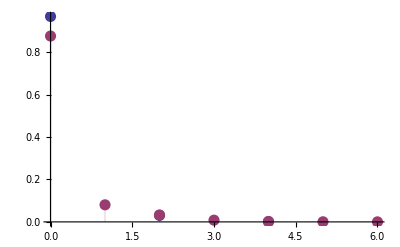

```mathematica
ListPlot[{ProbTeomAll[0.18],Table[{y-1,rho[[y,y]]},{y,1,n+1}]},PlotStyle-> {PointSize[0.02]},Filling->Axis, PlotRange->All]
```

```mathematica
(*reconstruct the Wigner function*)
```

```mathematica
Do[Rho[q,z]=rho[[q+1,z+1]],{q,0,n},{z,0,n}]
```

```mathematica
W[k_,l_,x_,y_]=(-1)^l/π*√((l!)/(k!))(√2*(x-ⅈ*y))^(k-l)*Exp[-(x^2+y^2)]*LaguerreL[l,k-l,2*(x^2+y^2)];
WMatrice[k_,l_,x_,y_]=If[k≥l,W[k,l,x,y],W[l,k,x,-y]]
Wigner[x_,y_]=∑_(k=0)^n ∑_(l=0)^n WMatrice[k,l,x,y]*Rho[k ,l];

Plot3D[Wigner[x,y],{x,-3,3},{y,-3,3},PlotRange->All]
```

If[k≥l,W[k,l,x,y],W[l,k,x,-y]]

-Graphics3D-

```mathematica
Laguerre[0,3,5.3]+LaguerreL[1,2,3.54]+LaguerreL[2,3,8.17]-LaguerreL[3,4,5.432]+LaguerreL[4,4,3.932]+LaguerreL[5,2,9.99]*LaguerreL[6,4,7.86]
```

1/2 (2+3 alpha+alpha^2-4 x-2 alpha x+x^2)